```mathematica
(*This is code from stackexchange http://mathematica.stackexchange.com/questions/18514/finding-face-vertices-from-the-face-adjacency-graph for counting the number of faces*)
(*=======================================================================================================*)
nextCandidate[s_,t_,adj_]:=Block[{length,pos},length=Length[adj];
pos=Mod[Position[adj,s][[1,1]]+1,length,1];
{t,adj[[pos]]}];

FindFace[g_?PlanarGraphQ]:=Block[{emb},emb=GraphEmbedding[g,"PlanarEmbedding"];
FindFace[g,emb]];

FindFace[g_?PlanarGraphQ,emb_]:=Block[{m,realvertexlist,fakevertexlist,tofakenums,torealnums,orderings,pAdj,rightF,s,t,initial,face,answers,outputfaces},
m=AdjacencyMatrix[g];
realvertexlist=VertexList[g];
fakevertexlist=Range[Length[realvertexlist]];
tofakenums=MapThread[Rule,{realvertexlist,fakevertexlist}];
torealnums=Map[Reverse,tofakenums];
Table[pAdj[v]=SortBy[Pick[fakevertexlist,m[[v]],1],ArcTan@@(emb[[v]]-emb[[#]])&],{v,fakevertexlist}];
rightF[_]:=False;
answers=Reap[Table[If[!rightF[e],s=e[[1]];
t=e[[2]];
initial=s;
face={s};
While[t=!=initial,rightF[UndirectedEdge[s,t]]=True;
{s,t}=nextCandidate[s,t,pAdj[t]];
face=Join[face,{s}];];
Sow[face];],{e,(EdgeList[g]/.tofakenums)}]][[2]];
If[answers=={},
outputfaces=answers/.torealnums;
,outputfaces=answers[[1]]/.torealnums;
];
outputfaces]
(*=======================================================================================================*)
allTestPlanarityQ[{aa_,bb_,cc_,dd_},bftlabeling_]:=Block[{a,b,c,d,planaritycollapsed,graph,externalnodes,choppedgraph,connectedcomponents,internalfaces,internalfacenodes,externaledges,whichfacescouldyoubein,howmanyfacescanyoubein,numcommonfaces},
planaritycollapsed=planarityQ[aa,bb,cc,dd];
{a,b,c,d}={aa,bb,cc,dd}//.{firstmat_,secondmat_,thirdmat_,fourthmat_}:>simplifyGraph[firstmat,(secondmat/.Map[#->0&,Flatten[Map[#[[2;;]]&,Cases[Map[Variables,secondmat],zz_/;Length[zz]>1]]]]),Function[{thebottomleft},Block[{output},If[Length[thebottomleft]>0,output=thebottomleft/.Map[#->0&,Flatten[Map[#[[2;;]]&,Cases[Map[Variables,Transpose[thebottomleft]],zz_/;Length[zz]>1]]]];,output=thebottomleft;];output]][thirdmat],fourthmat];
graph=turnIntoGraph[a,b,c,d,False];
If[PlanarGraphQ[graph],
externalnodes=getOrderingExternalNodesDefault[a,b,c,d];
choppedgraph=Graph[turnIntoGraph[Sequence@@({a,b,c,d}/.Map[#->0&,Variables[{b,c}]]),False],GraphLayout->"PlanarEmbedding"];
connectedcomponents=Map[Subgraph[choppedgraph,#]&,DeleteCases[ConnectedComponents[choppedgraph],{Alternatives@@externalnodes}]];
internalfacenodes=DeleteCases[Map[FindFace,connectedcomponents],zz_/;Length[zz]≤1];
internalfacenodes=DeleteCases[Append[Join@@internalfacenodes[[All,;;-2]],Join@@internalfacenodes[[All,-1]]],{}];
externaledges=Cases[EdgeList[graph],UndirectedEdge[Alternatives@@externalnodes,_]|UndirectedEdge[_,Alternatives@@externalnodes]];
whichfacescouldyoubein=Map[DeleteDuplicates[(#/.{}->Table[{ii,ii},{ii,(Length[internalfacenodes]/.{0->1})}])[[All,1]]]&,Map[Position[internalfacenodes,Alternatives@@#]&,externaledges]];
If[whichfacescouldyoubein=={},
numcommonfaces=1;
,numcommonfaces=Length[Intersection@@whichfacescouldyoubein];
];
If[planaritycollapsed===True,
If[numcommonfaces==0,
Print["kast=",{a,b,c,d}," : There's a problem with planarityQ! We are on genus zero on a graph declared planar, and yet we don't have that B=1."];
];
,If[numcommonfaces≥1,
Print["kast=",{a,b,c,d}," : There's a problem with planarityQ! We are on genus zero on a graph declared nonplanar, and yet we have that B=1."];
];
];
,If[planaritycollapsed=!=False,
Print["kast=",{a,b,c,d}," : There's a problem with planarityQ! When we don't collapse bivalent nodes, it gives that this example is planar even though it can't even be embedded on genus zero."];
];
];
];
DistributeDefinitions[allTestPlanarityQ];
```

```mathematica
ParallelMap[allTestPlanarityQ[#,True]&,Cases[annoyingsmallexamples,zz_/;(perfectMatchings@@zz)≠{}]];
```

```mathematica
ParallelMap[allTestPlanarityQ[#,True]&,allbft1kasteleyns];
```

kast={{{X[2,3],X[3,1],X[1,2],0},{X[4,2],X[1,4],0,0},{0,0,X[2,5],X[6,2]},{0,0,X[5,1],X[1,6]}},{{0,0,0},{0,0,Y[2,1]},{X[5,6],0,0},{0,X[6,5],0}},{{X[3,4],0,0,0},{0,X[4,3],0,0},{0,0,0,X[2,1]}},{{0,0,0},{0,0,0},{0,0,0}}} : There's a problem with planarityQ! We are on genus zero on a graph declared planar, and yet we don't have that B=1.

$Aborted

```mathematica
ParallelMap[allTestPlanarityQ[#,Null]&,allbft2kasteleyns];
```

```mathematica
ParallelMap[allTestPlanarityQ[#,False]&,allscatteringkasteleyns];
```

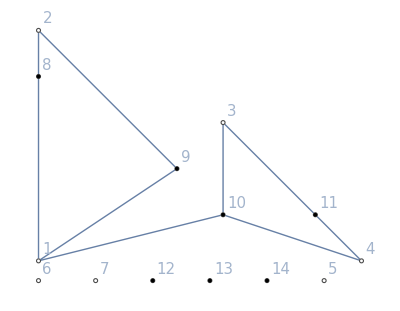

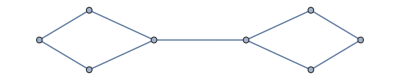

{{{1,8,2,9},{1,9,2,8},{1,10,4,11,3,10},{10,3,11,4}}}

{{1,8,2,9},{1,9,2,8},{1,10,4,11,3,10},{10,3,11,4}}

{{1,2},{3,4},{3,4},{1,2},{1,2},{3,4}}

```mathematica
{aa,bb,cc,dd}={{{X[2,3],X[3,1],X[1,2],0},{X[4,2],X[1,4],0,0},{0,0,X[2,5],X[6,2]},{0,0,X[5,1],X[1,6]}},{{0,0,0},{0,0,Y[2,1]},{X[5,6],0,0},{0,X[6,5],0}},{{X[3,4],0,0,0},{0,X[4,3],0,0},{0,0,0,X[2,1]}},{{0,0,0},{0,0,0},{0,0,0}}};
planaritycollapsed=planarityQ[aa,bb,cc,dd];
{a,b,c,d}={aa,bb,cc,dd}//.{firstmat_,secondmat_,thirdmat_,fourthmat_}:>simplifyGraph[firstmat,(secondmat/.Map[#->0&,Flatten[Map[#[[2;;]]&,Cases[Map[Variables,secondmat],zz_/;Length[zz]>1]]]]),Function[{thebottomleft},Block[{output},If[Length[thebottomleft]>0,output=thebottomleft/.Map[#->0&,Flatten[Map[#[[2;;]]&,Cases[Map[Variables,Transpose[thebottomleft]],zz_/;Length[zz]>1]]]];,output=thebottomleft;];output]][thirdmat],fourthmat];
graph=turnIntoGraph[a,b,c,d,False];
externalnodes=getOrderingExternalNodesDefault[a,b,c,d];

choppedgraph=Graph[turnIntoGraph[Sequence@@({a,b,c,d}/.Map[#->0&,Variables[{b,c}]]),False],GraphLayout->"PlanarEmbedding"]
connectedcomponents=Map[Subgraph[choppedgraph,#]&,DeleteCases[ConnectedComponents[choppedgraph],{Alternatives@@externalnodes}]]
internalfacenodes=DeleteCases[Map[FindFace,connectedcomponents],zz_/;Length[zz]≤1]
internalfacenodes=DeleteCases[Append[Join@@internalfacenodes[[All,;;-2]],Join@@internalfacenodes[[All,-1]]],{}]

externaledges=Cases[EdgeList[graph],UndirectedEdge[Alternatives@@externalnodes,_]|UndirectedEdge[_,Alternatives@@externalnodes]];
whichfacescouldyoubein=Map[DeleteDuplicates[(#/.{}->Table[{ii,ii},{ii,(Length[internalfacenodes]/.{0->1})}])[[All,1]]]&,Map[Position[internalfacenodes,Alternatives@@#]&,externaledges]]
```